## Roller coaster design - help file Copyright APCaBLab Amusement Park Honor Code applies! Execute cells from top down to see the development of a track with a loop

```mathematica
g=9.8;

length=300; 
v[y_,hi_]:=√(2g(hi-y))  (* speed at anypoint from change in height of track, y can be from a function y[x] *)
```

### Sample track in parametric format (it could be y[x] at this point, but it will have to be parametric when we cut in the loop)

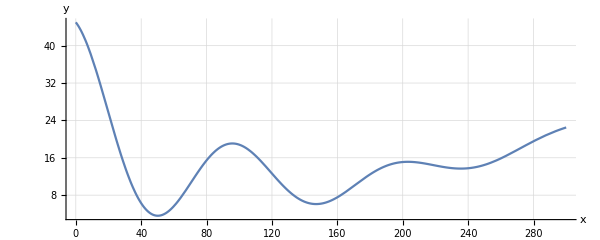

```mathematica
Clear[x,y];
x[t_]:=t
(* this is the height function -- change it *)
y[x_]:=(25+20Cos[Pi x/50])ⅇ^(-x/100)+.000225 x^2
hi=y[x[0]];
(* to make the y vs x plot shown below, we 'call' the y function with y[x[t]] *)

ParametricPlot[{x[t],y[x[t]]},{t,0,300},PlotRange->All,AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"x","y"},ImageSize->600]
```

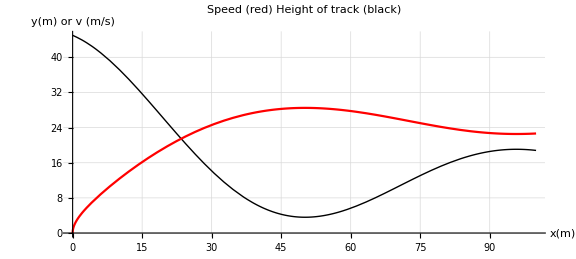

```mathematica
(* graph the track height along with speed as functions of x for the first minimum *)
tempLength=100;
Show[
ParametricPlot[{x[t],y[x[t]]},{t,0,tempLength},AxesOrigin->{0,0},PlotStyle->{Thick,Black}],
ParametricPlot[{x[t],v[y[x[t]],hi]},{t,0,tempLength},PlotStyle->Red],
AxesLabel->{"x(m)","y(m) or v (m/s)"},PlotLabel->"Speed (red)\n Height of track (black)",PlotRange->{{0,tempLength},All},GridLines->Automatic,ImageSize->Large
]
```

## Find the first local minimum

```mathematica
(* x=50 is a guess based on the above graph, you may have to change it *)
guess=50;
{cutX=x/.FindRoot[D[y[x],x]==0,{x,guess}],cutY=y[cutX]}
```

{50.1613,3.59452}

```mathematica
(* we now have the x,y point at which our track will be cut and the loop inserted *)
```

### find slope of track dy/dx on the downhill portion before the first minimum

```mathematica
slope[tee_]:=(180/Pi) ArcTan[D[y[t],t]/D[x[t],t]/.t->tee]//N
```

Max down slope = -50.7877° is too steep! Have to fix that.

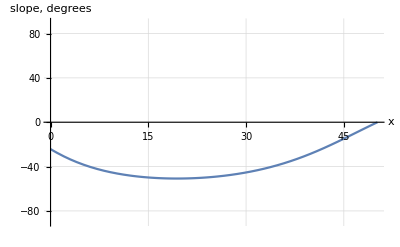

```mathematica
maxSlope=First@FindMinimum[slope[tee],{tee,10}]//Quiet;
If[Abs[maxSlope]>45,"Max down slope = "<>ToString[maxSlope]<>"° is too steep! Have to fix that. "]
Plot[slope[tee],{tee,0,minX},PlotRange->{-90,90},AxesLabel->{"x","slope, degrees"},GridLines->Automatic]
```

### inserting a cycloid loop at the base of the first hill

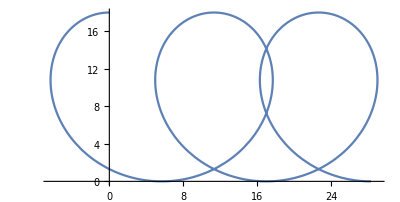

```mathematica
(* first define the cycloid parametrically and look at it *)
Clear[r,b];
cycloid[t_]:={r(t-Sin[b t]),r(1+Cos[b t])} (* returns a vector {x, y} *)
ParametricPlot[cycloid[t]/.r->9/.b->5,{t,0,Pi}]
```

```mathematica
(* the part of the loop we want starts at the first min and ends at the next min.  From solving dy/dx=0 for t for the cycloid, we can see that this runs from 
 t = Pi/b to  t = 3Pi/b; if we wanted a double loop, we'd continue to 5Pi/b. *)
```

```mathematica
dee=D[cycloid[t],t];
dydx=dee[[2]]/dee[[1]]
```

-(b Sin[b t])/(1-b Cos[b t])

```mathematica
(* find the horizontal tangent values of t *)
t/.Solve[dee[[2]]==0,t]/.C[1]->{0,1}
```

{{0,(2 π)/b},{π/b,(3 π)/b}}

Loop entry t = π/5  loop exit t = (3 π)/5

the loop is (18 π)/5 across

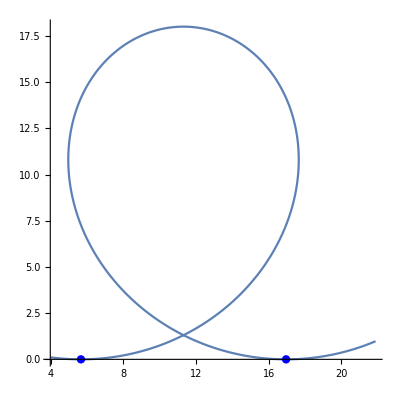

```mathematica
(* Note: all these t values give horizontal tangents,but we want the latter 2 because we're inserting the loop at a local minimum *)

r=9;b=5; (* sample values, which you will want to change *)
(* entry and exit points on the loop *)
startLoop=Pi/b;endLoop=3Pi/b;
(* the difference in the first components of cycloid at each point = the horizontal distance required for the loop *)
loopWidth=First@(cycloid[endLoop]-cycloid[startLoop]);
loopCenterX=First@cycloid[startLoop]+loopWidth/2;
Print["Loop entry t = ",startLoop,"  loop exit t = ",endLoop]
Print["the loop is ",loopWidth," across"]
(* show it *)
Show[
ParametricPlot[cycloid[t],{t,.95startLoop,1.05 endLoop }],
Graphics[{
{PointSize[.015],Blue,Point[cycloid[startLoop]],Point[cycloid[endLoop]]}
}]
]
```

### Plot with the loop inserted into a cut in the original track

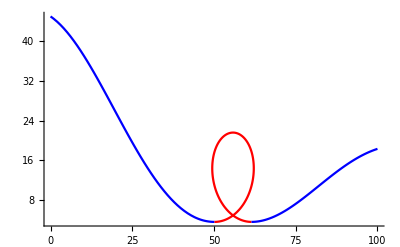

```mathematica
Show[
Plot[y[x],{x,0,cutX},PlotStyle->Blue],
ParametricPlot[cycloid[t]-cycloid[startLoop]+{cutX,cutY},{t,startLoop,endLoop},PlotStyle->Red],
Plot[y[x-loopWidth],{x,cutX+loopWidth,tempLength},PlotStyle->Blue],
PlotRange->All
]
(* adding the position of the first min {minX,minY} to the cycloid matches these parts of the track *)
```

### Build the piecewise parametric functions for the track by scaling the argument of the cycloid function to run from t=Pi/b to t=3Pi/b as x covers loopwidth

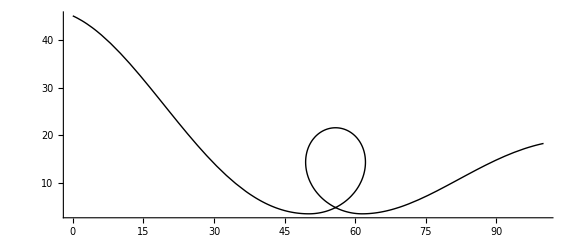

```mathematica
(* exx is the x coordinate of the final track. It is a function of t because it includes the parametric cycloid.  
The track is defined in pieces using Mathematica's conditional definition /; meaning 'where' *)

exx[t_]:=x[t]/;t<minX (* portion before the loop starts, where x is just t *)
exx[t_]:=First@(cycloid[Pi/b+(2Pi)/b(t-minX)/loopWidth]-cycloid[startLoop])+minX/;minX≤ t<minX+loopWidth (* this part is the loop itself: 
when t=minX, we start the loop as if t= Pi/b,
when t=minX+loopWidth, we are leaving the loop as if t= 3Pi/b  *)

exx[t_]:=x[t]/;t≥ minX+loopWidth (* after the loop ends we're on the original track, shifted by loopWidth *)

(* wye coordinate is a function of position x (it will actually be x[t] when used) *)

wye[x_]:=y[x]/;x≤ minX (* the original y function prior to the loop *)
wye[x_]:=Last@(cycloid[Pi/b+(2Pi)/b(x-minX)/loopWidth]-cycloid[startLoop])+minY/;minX<x≤ minX+loopWidth
wye[x_]:=y[x-loopWidth]/;x>minX+loopWidth (* the original y function after the loop *)

(* plot it *)
ParametricPlot[{exx[t],wye[x[t]]},{t,0,tempLength},PlotStyle->{Thick,Black},PlotRange->All,AspectRatio->Automatic,AxesOrigin->{0,0},ImageSize->Large]
```

### Show the velocity graph and check acceleration at the top of the loop

Speed required at top of loop = 7.4 m/s

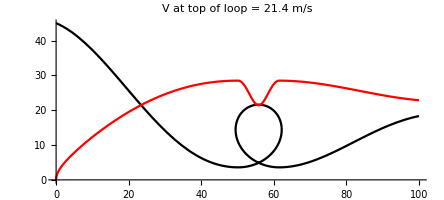

acceleration = 81.1243 m/s^2 or 8.3 gees

Fail: You just killed the riders! Change r and b or slow it down!

```mathematica
(* guess the radius is loopWidth/2 *)
radius=loopWidth/2;
Print["Speed required at top of loop = ",Round[√(g radius),.1]," m/s"]
Show[
ParametricPlot[{exx[t],wye[x[t]]},{t,0,tempLength},PlotStyle->Black],
Plot[v[wye[x],hi],{x,0,tempLength},PlotStyle->Red],PlotLabel->Style["V at top of loop = "<>ToString@Round[v[wye[minX+loopWidth/2],hi],.1]<>" m/s",14]
]


(* acceleration *)

Print["acceleration = ",ac=v[wye[minX+loopWidth/2],hi]^2/radius," m/s^2 or ",Round[ac/g,.1]," gees"]

Which[ac/g<4.5,Style["Loop is passable",Green,14],
4.5≤ac/ g<5.5,Style["Warning: acceleration is too high, riders are unconscious",Blue,14],
ac/g≥5.5 ,Style["Fail: You just killed the riders! Change r and b or slow it down!",Red,14]
]
```

```mathematica
(* To experiment with track designs (for fun),see http://www.lineflyer1.net/  *)
```